# Ionization wave

## Cartoon

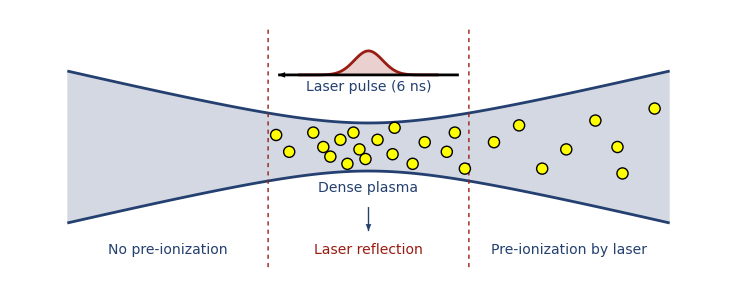

```mathematica
(* -- laser envelope functions -- *)
w0=1;
zR=10;
w[z_]:=N[w0 √(1+(z/zR)^2)];
a=1;
b=2;
c=3;
pulse[z_]:=a Exp[-(z/b)^2]+c;

(* -- discrete data points -- *)
dt={
Table[{z,w[z]},{z,-30,30,.1}],
Table[{z,-w[z]},{z,-30,30,.1}],
Table[{z,pulse[z]},{z,-7,7,.1}]
};

(* -- electrons -- *)
pts={
{-9.2,.5},{-7.9,-.2},{-5.5,.6},{-4.5,0},{-3.8,-.4},{-2.8,.3},{-1.5,.6},{-.9,-.1},{-.3,-.5},{-2.1,-.7},{0.9,.3},{2.6,.8},{2.4,-.3},{4.4,-.7},{5.6,.2},{7.8,-.2},{8.6,0.6},{9.6,-.9},{12.5,.2},{15,.9},{17.3,-.9},{19.7,-.1},{22.6,1.1},{25.3,-1.1},{24.8,0},{28.5,1.6}
};

(* -- plot -- *)
gf=ListLinePlot[

dt,

Epilog->{
{Black,AbsoluteThickness[2],Arrowheads[{0,.03}],Arrow[{{9,c},{-9,c}}]},
Text[Style["Laser pulse (6 ns)",FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain],{0,c-.2},{0,1}],
{RGBColor[.60,.11,.07,1],AbsoluteThickness[1],AbsoluteDashing[3],Line[{{10,-5},{10,5}}]},
{RGBColor[.60,.11,.07,1],AbsoluteThickness[1],AbsoluteDashing[3],Line[{{-10,-5},{-10,5}}]},
Text[Style["Dense plasma",FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain],{0,-2},{0,-1}],
{RGBColor[.14,.25,.44,1],AbsoluteThickness[1],Arrowheads[{0,.02}],Arrow[{{0,-2.5},{0,-3.5}}]},
Text[Style["Laser reflection",FontColor->RGBColor[.60,.11,.07,1],FontSize->14,FontWeight->Plain],{0,-4},{0,1}],
Text[Style["No pre-ionization",FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain],{-20,-4},{0,1}],
Text[Style["Pre-ionization by laser",FontColor->RGBColor[.14,.25,.44,1],FontSize->14,FontWeight->Plain],{20,-4},{0,1}],
{EdgeForm[{Black,AbsoluteThickness[1]}],FaceForm[{Yellow}],Disk[#,Offset[4]]}&/@pts
},

Joined->True,
PlotRange->{{-30,30},{-5,5}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},

PlotStyle->{
{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2]},
{RGBColor[.60,.11,.07,1],Opacity[1],AbsoluteThickness[2]}
},

Axes->False,
Frame->False,
GridLines->None,

ImagePadding->0,
ImageSize->(130*2)*(72/25.4),
AspectRatio->.4,

Filling->{1->{2},3->c}

];

Print[gf];

Export[NotebookDirectory[]<>"ionizationWave.pdf",gf];
```